```mathematica
Table[
{tuple, CalcGoodForTuple[tuple,1000000]},
{tuple,Select[
Prime[Subsets[Range[2,10],{4}]],
magicGraham[#]>0&]}
]
```

LinkObject::linkd: Unable to communicate with closed link LinkObject[.

KernelObject::rdead: Subkernel connected through local appears dead.

LinkObject::linkd: Unable to communicate with closed link LinkObject[.

KernelObject::rdead: Subkernel connected through local appears dead.

LinkObject::linkd: Unable to communicate with closed link LinkObject[.

General::stop: Further output of LinkObject will be suppressed during this calculation.

KernelObject::rdead: Subkernel connected through local appears dead.

General::stop: Further output of KernelObject will be suppressed during this calculation.

ParallelTable::nopar: No parallel kernels available; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable will be suppressed during this calculation.

Aborted at value : 16864

$Aborted

```mathematica
N[magicGraham[{3,31,43,173,229}]]
```

2.08745×10^-7

```mathematica
CalcGoodForTuple[{3,31,43,173,229},100000]
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\Solutions.txt.54.28%.
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\31\43\173\229\Solutions.txt.63.82%.
```

```mathematica
66.29
```

```mathematica
67.24
```

```mathematica
73.01%
```

```mathematica
73.98
```

```mathematica
74.36
```

```mathematica
74.59
```

```mathematica
8.363
```

```mathematica
8.426
```

```mathematica
9.449%
```

```mathematica
10.086%
```

```mathematica
10.221
```

```mathematica
10.31
```

```mathematica
10.325
```

```mathematica
10.536%.-2236
```

```mathematica
10.605%.-2236
```

```mathematica
11.249%.-2236
```

```mathematica
11.249%.-2323
```

```mathematica
11.249%.-2348
```

```mathematica
11.249%.-2379
```

```mathematica
11.249%.-2452
```

```mathematica
11.258%.-2452
```

```mathematica
11.472%.-2452
```

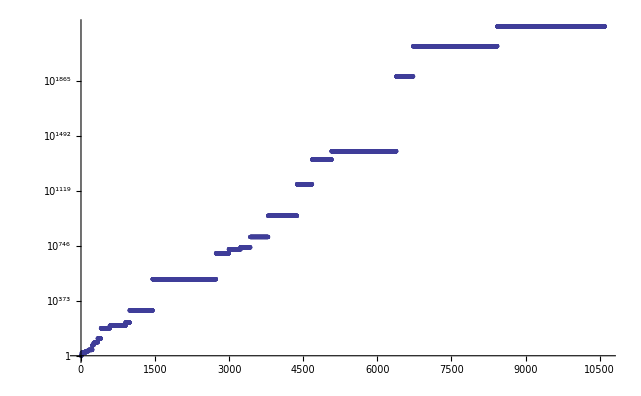

```mathematica
ListLogPlot[GoodForTuple[{3,31,43,173,229}],PlotRange->All]
```

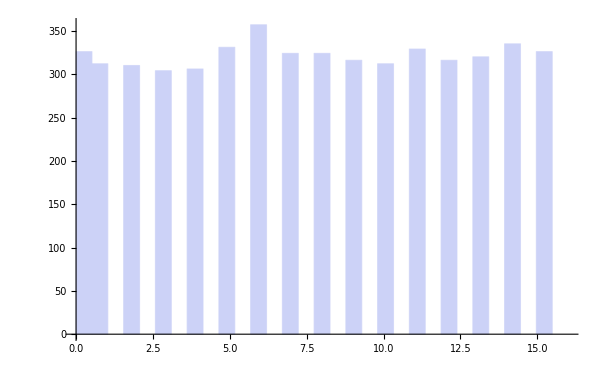

```mathematica
Histogram[Map[Mod[#,31]&,GoodForTuple[{3,31,43,173,229}]],31]
```